# Comparison of Histograms

## Histogram 1: 1,000 events generated

```mathematica
data = Import["/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/examples/top-quark-data.dat"] ;
```

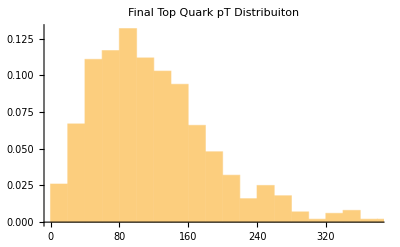

```mathematica
Histogram[data[[All, 1]], Automatic, "Probability", PlotLabel->HoldForm[Final Top Quark pT Distribuiton]]
```

```mathematica
data = Import["/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/examples/top-quark-data.dat"];
```

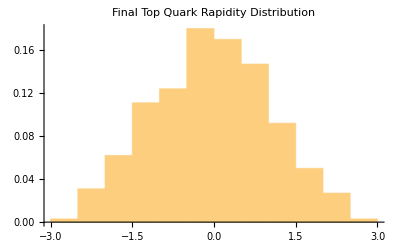

```mathematica
Histogram[data[[All, 2]], Automatic, "Probability", PlotLabel-> HoldForm[Final Top Quark Rapidity Distribution]]
```

## Histogram 2: 10,000 events generated

```mathematica
data = Import["/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/pythia8240/examples/test-Output.dat"];
```

```mathematica
Histogram[data[[All, 1]], Automatic, "Probability"]
```

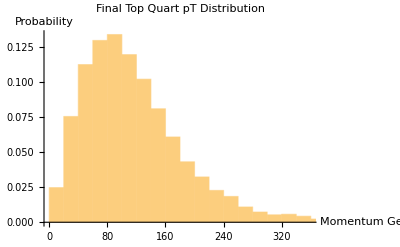

```mathematica
Show[%12,AxesLabel->{HoldForm[Momentum GeV],HoldForm[Probability]},PlotLabel->HoldForm[Final Top Quart pT Distribution],LabelStyle->{GrayLevel[0],Bold}]
```

## Histogram 3: 100,000 events generated

```mathematica
data = Import["/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/pythia8240/examples/test-Output.dat"];
```

```mathematica
Histogram[data[[All, 1]], Automatic, "Probability"]
```

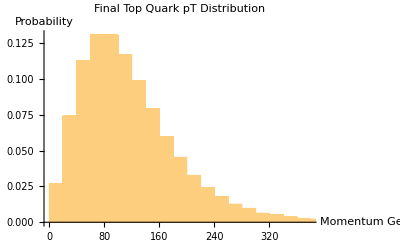

```mathematica
Show[%15,AxesLabel->{HoldForm[Momentum GeV],HoldForm[Probability]},PlotLabel->HoldForm[Final Top Quark pT Distribution],LabelStyle->{GrayLevel[0],Bold}]
```

## Histogram 4: 1,000,000 events generated

```mathematica
data = Import["/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/pythia8240/examples/test-Output.dat"];
```

```mathematica
Histogram[data[[All, 1]], Automatic, "Probability"]
```

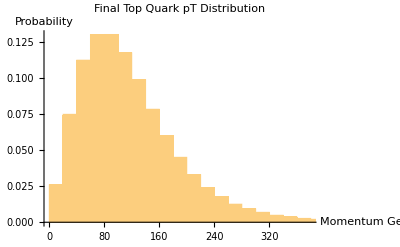

```mathematica
Show[%18,AxesLabel->{HoldForm[Momentum GeV],HoldForm[Probability]},PlotLabel->HoldForm[Final Top Quark pT Distribution],LabelStyle->{GrayLevel[0],Bold}]
```